```mathematica
(* some basis vectors *)
𝕖ρp={Cos[φp],Sin[φp],0};
𝕖ρ={Cos[φ],Sin[φ],0};
𝕖z={0,0,1};
```

```mathematica
(* position vectors for surface and point in space *)
R[k_]:={Ri,Ro}[[k]]
𝕩=ρ*𝕖ρ+z*𝕖z;
𝕩p[k_]:=R[k]*𝕖ρp+zp*𝕖z;
```

```mathematica
𝕕=𝕩-𝕩p[1];
𝕕in𝕕=Dot[𝕕,𝕕];
integrand=1/Sqrt[𝕕in𝕕]
```

1/(√((z-zp)^2+(ρ Cos[φ]-Ri Cos[φp])^2+(ρ Sin[φ]-Ri Sin[φp])^2))

```mathematica
intZ=Integrate[R[1]*integrand,φp]//Simplify
```

-(2 Ri √((Ri^2+z^2-2 z zp+zp^2+ρ^2-2 Ri ρ Cos[φ-φp])/(Ri^2+z^2-2 z zp+zp^2-2 Ri ρ+ρ^2)) EllipticF[(φ-φp)/2,-(4 Ri ρ)/(Ri^2+z^2-2 z zp+zp^2-2 Ri ρ+ρ^2)])/(√(Ri^2+z^2-2 z zp+zp^2+ρ^2-2 Ri ρ Cos[φ-φp]))

```mathematica
newIntegrand=(intZ/.{φp->α})-intZ/.{φp->-α}//Simplify
```

-(2 Ri √((Ri^2+z^2-2 z zp+zp^2+ρ^2-2 Ri ρ Cos[α-φ])/(Ri^2+z^2-2 z zp+zp^2-2 Ri ρ+ρ^2)) EllipticF[1/2 (-α+φ),-(4 Ri ρ)/(Ri^2+z^2-2 z zp+zp^2-2 Ri ρ+ρ^2)])/(√(Ri^2+z^2-2 z zp+zp^2+ρ^2-2 Ri ρ Cos[α-φ]))+(2 Ri √((Ri^2+z^2-2 z zp+zp^2+ρ^2-2 Ri ρ Cos[α+φ])/(Ri^2+z^2-2 z zp+zp^2-2 Ri ρ+ρ^2)) EllipticF[(α+φ)/2,-(4 Ri ρ)/(Ri^2+z^2-2 z zp+zp^2-2 Ri ρ+ρ^2)])/(√(Ri^2+z^2-2 z zp+zp^2+ρ^2-2 Ri ρ Cos[α+φ]))

```mathematica
intZ=Integrate[newIntegrand,zp]
```

∫(-(2 Ri √((Ri^2+z^2-2 z zp+zp^2+ρ^2-2 Ri ρ Cos[α-φ])/(Ri^2+z^2-2 z zp+zp^2-2 Ri ρ+ρ^2)) EllipticF[1/2 (-α+φ),-(4 Ri ρ)/(Ri^2+z^2-2 z zp+zp^2-2 Ri ρ+ρ^2)])/(√(Ri^2+z^2-2 z zp+zp^2+ρ^2-2 Ri ρ Cos[α-φ]))+(2 Ri √((Ri^2+z^2-2 z zp+zp^2+ρ^2-2 Ri ρ Cos[α+φ])/(Ri^2+z^2-2 z zp+zp^2-2 Ri ρ+ρ^2)) EllipticF[(α+φ)/2,-(4 Ri ρ)/(Ri^2+z^2-2 z zp+zp^2-2 Ri ρ+ρ^2)])/(√(Ri^2+z^2-2 z zp+zp^2+ρ^2-2 Ri ρ Cos[α+φ])))ⅆzp

```mathematica
Integrate[R[1]*integrand,{zp,-d,d}]
```

$Aborted

```mathematica
Integrate[R[1]/integrand,{φp,-α,α},{zp,-d,d},Assumptions->{d>0,0<α≤π,ρ>0,Ri>0,Ro>0,φp∈Reals,φ∈Reals,zp∈Reals,z∈Reals,Ro>Ri}]
```

$Aborted

```mathematica
Vm=M0/4/π*Sum[
(-1)^k*Integrate[R[k]/Norm[𝕩-𝕩p[k]],{φp,-α,α},{zp,-d,d}],
{k,1,2}
]
```

$Aborted

```mathematica
VmCart=ReplaceAll[Vm,ρ->Sqrt[x^2+y^2]]//Simplify;
```

```mathematica
H=-Grad[VmCart,{x,y,z}];
```

```mathematica
padx=2;
pady=2;

wVal=1/2;
dVal=1/2;

αVal=π/4;
RmVal=4;
RiVal=3.5;
RoVal=4.5;
```

```mathematica
padR=1;
canvas=Rectangle[{0,-RmVal},{2RmVal,RmVal}];

magnetSegment=RegionDifference[Disk[{0,0},RmVal+wVal,{-αVal,αVal}],
Disk[{0,0},RmVal-wVal,{-αVal,αVal}]];
```

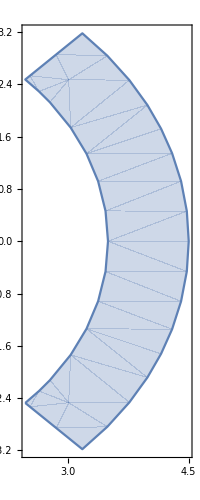

```mathematica
RegionPlot[magnetSegment,AspectRatio->Automatic]
```

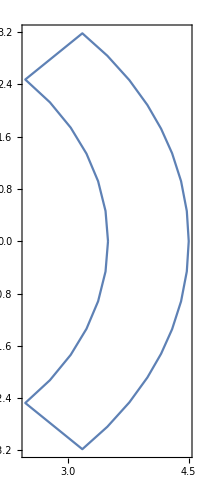

```mathematica
magnetSegmentBoundary =RegionUnion[
Circle[{0,0},RmVal+wVal,{-αVal,αVal}],
Circle[{0,0},RmVal-wVal,{-αVal,αVal}],
Line[{{(RmVal-wVal)*Cos[αVal],(RmVal-wVal)*Sin[αVal]},{(RmVal+wVal)*Cos[αVal],(RmVal+wVal)*Sin[αVal]}}],
Line[{{(RmVal-wVal)*Cos[-αVal],(RmVal-wVal)*Sin[-αVal]},{(RmVal+wVal)*Cos[-αVal],(RmVal+wVal)*Sin[-αVal]}}]
];
RegionPlot[magnetSegmentBoundary,AspectRatio->Automatic]
```

```mathematica
pars={d->dVal,z->1, α->αVal,Ri->RiVal,Ro->RoVal,M0->1};
Hplot[x_,y_]=H/.pars;
```

```mathematica
Hplot[x,y]
```

{-1/(4 π)(-5.49779 ((x (3.5-√(x^2+y^2)))/(√(x^2+y^2) √(1/4+(3.5-√(x^2+y^2))^2) (1/2+√(1/4+(3.5-√(x^2+y^2))^2)))-(x (3.5-√(x^2+y^2)))/(√(x^2+y^2) √(9/4+(3.5-√(x^2+y^2))^2) (3/2+√(9/4+(3.5-√(x^2+y^2))^2))))+7.06858 ((x (4.5-√(x^2+y^2)))/(√(x^2+y^2) √(1/4+(4.5-√(x^2+y^2))^2) (1/2+√(1/4+(4.5-√(x^2+y^2))^2)))-(x (4.5-√(x^2+y^2)))/(√(x^2+y^2) √(9/4+(4.5-√(x^2+y^2))^2) (3/2+√(9/4+(4.5-√(x^2+y^2))^2))))),-1/(4 π)(-5.49779 ((y (3.5-√(x^2+y^2)))/(√(x^2+y^2) √(1/4+(3.5-√(x^2+y^2))^2) (1/2+√(1/4+(3.5-√(x^2+y^2))^2)))-(y (3.5-√(x^2+y^2)))/(√(x^2+y^2) √(9/4+(3.5-√(x^2+y^2))^2) (3/2+√(9/4+(3.5-√(x^2+y^2))^2))))+7.06858 ((y (4.5-√(x^2+y^2)))/(√(x^2+y^2) √(1/4+(4.5-√(x^2+y^2))^2) (1/2+√(1/4+(4.5-√(x^2+y^2))^2)))-(y (4.5-√(x^2+y^2)))/(√(x^2+y^2) √(9/4+(4.5-√(x^2+y^2))^2) (3/2+√(9/4+(4.5-√(x^2+y^2))^2))))),-(-5.49779 (-(1+1/(2 √(1/4+(3.5-√(x^2+y^2))^2)))/(1/2+√(1/4+(3.5-√(x^2+y^2))^2))+(1+3/(2 √(9/4+(3.5-√(x^2+y^2))^2)))/(3/2+√(9/4+(3.5-√(x^2+y^2))^2)))+7.06858 (-(1+1/(2 √(1/4+(4.5-√(x^2+y^2))^2)))/(1/2+√(1/4+(4.5-√(x^2+y^2))^2))+(1+3/(2 √(9/4+(4.5-√(x^2+y^2))^2)))/(3/2+√(9/4+(4.5-√(x^2+y^2))^2))))/(4 π)}

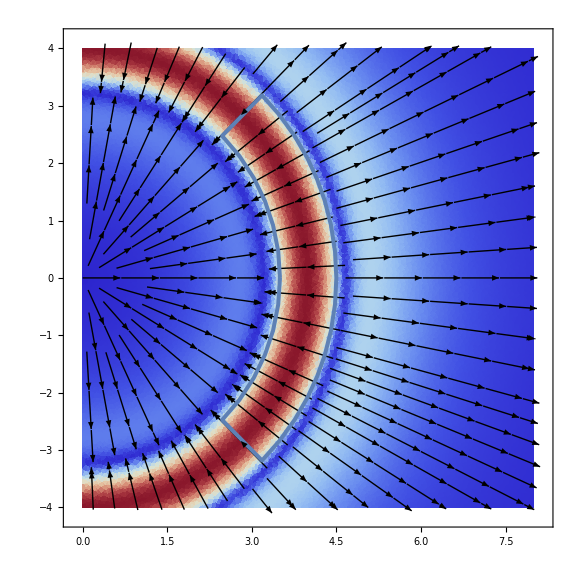

```mathematica
(* plot free current potential *)
segment=Show[
StreamDensityPlot[Evaluate@Hplot[x,y][[{1,2}]],{x,y}∈canvas,ColorFunction->ColorData["ThermometerColors"], StreamStyle->Black,StreamColorFunction->None,AspectRatio->Automatic],
RegionPlot[magnetSegmentBoundary,BoundaryStyle->{Thickness[0.005]}],
ImageSize->Large,Axes->False
]
```

```mathematica
(* plot free current potential *)
segment=Show[
StreamDensityPlot[Evaluate@Hplot[x,y][[{1,2}]],{x,y}∈canvas,ColorFunction->ColorData["ThermometerColors"], StreamStyle->Black,StreamColorFunction->None,AspectRatio->Automatic],
ImageSize->Large,Axes->False
]
```

-Graphics-